```mathematica
(* IMPORT MODULES *)
ClearAll[m1,m2,m3]
loadDumpSaves=True;
SetDirectory[NotebookDirectory[]];
NotebookEvaluate["modules/oscillator_bracket.nb"];
NotebookEvaluate["modules/mews_and_alphas.nb"];
NotebookEvaluate["modules/operators.nb"];
NotebookEvaluate["modules/hamiltonian.nb"];
NotebookEvaluate["modules/parameters.nb"];
NotebookEvaluate["modules/golden_search.nb"];
If[loadDumpSaves,NotebookEvaluate["modules/load_dump_saves.nb"]];
SetDirectory[NotebookDirectory[]];
```

```mathematica
(* For loop for calculating temperature curves *)
temps=Table[t,{t,0,1,0.1}];
dict=<|uq->"u",sq->"s",cq->"c",bq->"b"|>;
save=True;(* Do you want to save the results? *)

tData[J_,P_,flavourSym_,γMax_,Λ_,S_,mass1_,mass2_,mass3_,excited_]:=Module[
{tempData},
tempData={};
For[iter=1,iter≤Length[temps],iter++,
temp=temps[[iter]];
m1=mass1;(* mass of quark 1 *)
m2=mass2;(* mass of quark 2 *)
m3=mass3;(* mass of quark 3 *)
temperature=temp;

(* all different masses = 0, two equal masses = 1, all equal masses = 2 *)
case=If[m1==m2,1,0];
case=If[m1==m2==m3,2,case];
states=allStates[J,P,Λ,S,γMax];
sM=stateMatrix[J,P,Λ,S,γMax];

(* Calculate generalised transformation matrices *)
{t1time,t1}=AbsoluteTiming[tMatrix[J,P,Λ,S,γMax,m1,m2,m3,1]];
(*Print["Time taken to compute t1: ", ToString[t1time]];*)
{t2time,t2}=AbsoluteTiming[tMatrix[J,P,Λ,S,γMax,m1,m2,m3,2]];
(*Print["Time taken to compute t2: ", ToString[t2time]];*)
DumpSave["modules/dumpSave/summationVariables.mx",summationVariables];
DumpSave["modules/dumpSave/talmi.mx",talmi];

(* Obtain projector matrix *)
proj=projector[states,flavourSym,case];

(* Required matrices for hamiltonian *)
vCoulomb=polynomialOperatorRho[sM,-1];(* 1/ρ matrix dimensionless *)
vLinear=polynomialOperatorRho[sM,1];(* ρ matrix dimensionless *)
qhoSpect=qhoSpectrum[sM];
kineticRho=polynomialOperatorRho[sM,2];
kineticLam=polynomialOperatorLambda[sM,2];
ham[ω_]:=Hb[ω,temperature,m1,m2,m3,proj];

(* Find minimum and errors*)
{minTime,{a,b,data}}=AbsoluteTiming[goldenSearch[ham,excited+1,0.01,0.9,0.05]];
(*Print["Time taken to find minimum: ", ToString[minTime]];*)
wMin=(a+b)/2;
hamiltonian=ham[wMin];
eigvalMin=Eigenvalues[hamiltonian][[-excited-1]];
AppendTo[tempData,{temp,eigvalMin}];
Print[iter,". t = ", temp,", ω = ",wMin, ", E = ",eigvalMin];
(*Print["{ω_min, E_min}: ",{Around[wMin,a-wMin],eigvalMin}];
Print["Number of basis functions (matrix size): ", Length[hamiltonian]];*)
(* Dump Saves *)

DumpSave["modules/dumpSave/nineJ.mx",nineJ];
DumpSave["modules/dumpSave/rel.mx",rel];
DumpSave["modules/dumpSave/Rcoeff.mx",Rcoeff];
DumpSave["modules/dumpSave/Lcoeff.mx",Lcoeff];
](* End of For loop *);
Print[tempData];
tempData
]

temperatureData[J_,P_,flavourSym_,γMax_,Λ_,S_,mass1_,mass2_,mass3_,excited_]:=temperatureData[J,P,flavourSym,γMax,Λ,S,mass1,mass2,mass3,excited]=Module[{tempData},
tempData=tData[J,P,flavourSym,γMax,Λ,S,mass1,mass2,mass3,excited];
If[save&&NumberQ[tempData[[1,2]]],
DumpSave["modules/dumpSave/temperature_data.mx",tData];
Print["Saved temperature data successfully"],
Print["Data not saved"]
];
tempData
]
```

```mathematica
?temperatureData
```

## Comparing negative and positive parity states as function of T/T_c

1. t = 0., ω = 0.584849, E = 2.29291

2. t = 0.1, ω = 0.584849, E = 2.28875

3. t = 0.2, ω = 0.584849, E = 2.27611

4. t = 0.3, ω = 0.584849, E = 2.25451

5. t = 0.4, ω = 0.584849, E = 2.22302

6. t = 0.5, ω = 0.554196, E = 2.17983

7. t = 0.6, ω = 0.535251, E = 2.12239

8. t = 0.7, ω = 0.504598, E = 2.04573

9. t = 0.8, ω = 0.455, E = 1.93982

10. t = 0.9, ω = 0.405402, E = 1.7773

11. t = 1., ω = 0.034799, E = 1.17263

{{0.,2.29291},{0.1,2.28875},{0.2,2.27611},{0.3,2.25451},{0.4,2.22302},{0.5,2.17983},{0.6,2.12239},{0.7,2.04573},{0.8,1.93982},{0.9,1.7773},{1.,1.17263}}

Saved temperature data successfully

1. t = 0., ω = 0.405402, E = 2.66773

2. t = 0.1, ω = 0.405402, E = 2.6625

3. t = 0.2, ω = 0.405402, E = 2.64661

4. t = 0.3, ω = 0.405402, E = 2.61948

5. t = 0.4, ω = 0.405402, E = 2.57998

6. t = 0.5, ω = 0.374749, E = 2.52557

7. t = 0.6, ω = 0.355804, E = 2.45314

8. t = 0.7, ω = 0.325151, E = 2.35634

9. t = 0.8, ω = 0.294498, E = 2.22161

10. t = 0.9, ω = 0.2449, E = 2.01312

11. t = 1., ω = 0.034799, E = 1.19961

{{0.,2.66773},{0.1,2.6625},{0.2,2.64661},{0.3,2.61948},{0.4,2.57998},{0.5,2.52557},{0.6,2.45314},{0.7,2.35634},{0.8,2.22161},{0.9,2.01312},{1.,1.19961}}

Saved temperature data successfully

{{0.,2.66773},{0.1,2.66773},{0.2,2.66773},{0.3,2.66773},{0.4,2.66773},{0.5,2.66773},{0.6,2.66773},{0.7,2.66773},{0.8,2.66773},{0.9,2.66773},{1.,2.66773}}

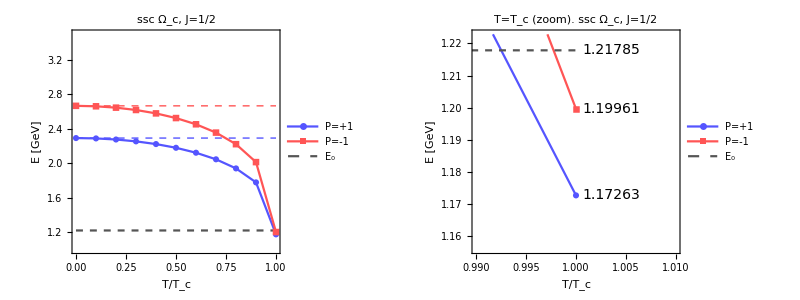

```mathematica
m1=uq;
m2=uq;
m3=cq;
fs=0;
gm=4;
excited=0;
pos=temperatureData[1/2,+1,fs,gm,0,1/2,m1,m2,m3,excited];
neg=temperatureData[1/2,-1,fs,gm,1,1/2,m1,m2,m3,excited];
imgSize=420;
imagePadding={{90,10},{45,10}};

SetOptions[ListPlot,
Frame->True,
Joined->True,
Axes->True,
FrameLabel->{"T/T_c","E [GeV]"},
PlotMarkers->{Automatic,Automatic,False,False,False},
ImagePadding->imagePadding,
ImageSize->imgSize,
PlotStyle->{Lighter[Blue],Lighter[Red],{Lighter[Black],Dashed},{Lighter[Blue],Dashed,Thin},{Lighter[Red],Dashed,Thin}},
LabelStyle->{FontFamily->"Arial",FontSize->14}];

plotLabels={pos[[-1,2]],neg[[-1,2]],m1+m2+m3-1/2(3Cqqq)};
plotPositions={{1.0005,pos[[-1,2]]},{1.0005,neg[[-1,2]]},{1.0005,m1+m2+m3-1/2(3Cqqq)}};
E0=m1+m2+m3-1/2(3Cqqq);
dashedLine=Table[{t,E0},{t,0,1,0.1}];
dashedPos=Table[{t,pos[[1,2]]},{t,0,1,0.1}];
dashedNeg=Table[{t,neg[[1,2]]},{t,0,1,0.1}]

main=ListPlot[{pos,neg,dashedLine,dashedPos,dashedNeg},
PlotLabel->"ssc Ω_c, J=1/2",
PlotLegends->Placed[{"P=+1","P=-1","E_0"},{Right,Top}],
PlotRange->{Automatic,{1,3.5}}
];

sub=ListPlot[{pos,neg,dashedLine,dashedPos},
PlotRange->{{0.99,1.01},{E0-0.062,E0+0.005}},
PlotLabels->Placed[plotLabels,plotPositions],
PlotLabel->"T=T_c (zoom). ssc Ω_c, J=1/2",
PlotLegends->Placed[{"P=+1","P=-1","E_0"},{Left,Bottom}]
];

grid=Grid[{{main,sub}}]
```

```mathematica
Export["plots/ch8_ssc_jhalf_pVSn.pdf",grid,"AllowRasterization"->True,ImageSize->360,ImageResolution->600]
```

plots/ch8_ssc_jhalf_pVSn.pdf

## Single baryon excited states as function of T/T_c

{{0.,2.62498},{0.1,2.62498},{0.2,2.62498},{0.3,2.62498},{0.4,2.62498},{0.5,2.62498},{0.6,2.62498},{0.7,2.62498},{0.8,2.62498},{0.9,2.62498},{1.,2.62498}}

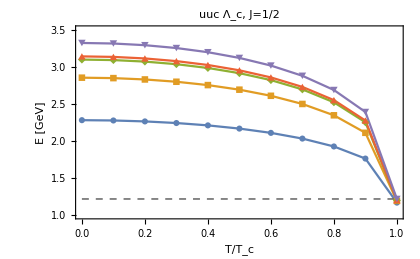
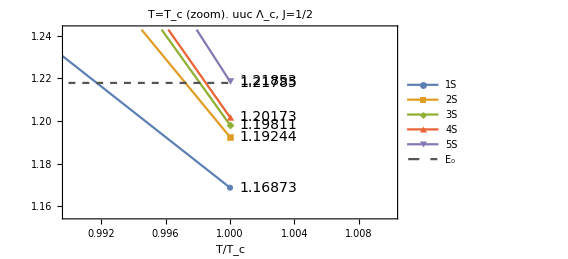
-Graphics- | -Graphics-

```mathematica
m1=uq;
m2=uq;
m3=cq;
fs=0;
gm=12;
pos1=temperatureData[1/2,+1,fs,gm,0,1/2,m1,m2,m3,0];
pos2=temperatureData[1/2,+1,fs,gm,0,1/2,m1,m2,m3,1];
pos3=temperatureData[1/2,+1,fs,gm,0,1/2,m1,m2,m3,2];
pos4=temperatureData[1/2,+1,fs,gm,0,1/2,m1,m2,m3,3];
pos5=temperatureData[1/2,+1,fs,gm,0,1/2,m1,m2,m3,4];
imgSize=420;
imagePadding={{50,10},{45,10}};

SetOptions[ListPlot,
Frame->True,
Joined->True,
Axes->True,
FrameLabel->{"T/T_c","E [GeV]"},
PlotMarkers->{Automatic,Automatic,Automatic,Automatic,Automatic,False},
ImagePadding->imagePadding,
ImageSize->imgSize,
PlotStyle->{{Automatic},{Automatic},{Automatic},{Automatic},{Automatic},{Lighter[Black],Dashed,Thin}},
LabelStyle->{FontFamily->"Arial",FontSize->14}];

plotLabels={pos1[[-1,2]],pos2[[-1,2]],pos3[[-1,2]],pos4[[-1,2]],pos5[[-1,2]],m1+m2+m3-1/2(3Cqqq)};
plotPositions={{1.0005,pos1[[-1,2]]},{1.0005,pos2[[-1,2]]},{1.0005,pos3[[-1,2]]},{1.0005,pos4[[-1,2]]},{1.0005,pos5[[-1,2]]},{1.0005,m1+m2+m3-1/2(3Cqqq)}};
E0=m1+m2+m3-1/2(3Cqqq);
dashedLine=Table[{t,E0},{t,0,1,0.1}];
dashedPos=Table[{t,pos[[1,2]]},{t,0,1,0.1}];
dashedNeg=Table[{t,neg[[1,2]]},{t,0,1,0.1}]

main=ListPlot[{pos1,pos2,pos3,pos4,pos5,dashedLine},
PlotLabel->"uuc Λ_c, J=1/2",

PlotRange->{Automatic,{1,3.5}}
];

sub=ListPlot[{pos1,pos2,pos3,pos4,pos5,dashedLine},
PlotRange->{{0.99,1.01},{E0-0.062,E0+0.025}},
PlotLabels->Placed[plotLabels,plotPositions],
PlotLegends->Placed[{"1S","2S","3S","4S","5S","E_0"},{After,Top}],
PlotLabel->"T=T_c (zoom). uuc Λ_c, J=1/2",
FrameLabel->{"T/T_c",""}
];

grid=Grid[{{main,sub}}]
```

```mathematica
Export["plots/ch8_uuc_ladder.pdf",grid,"AllowRasterization"->True,ImageSize->360,ImageResolution->600]
```

plots/ch8_uuc_ladder.pdf

## Expectation Values

```mathematica
hamiltonian=1
eigenvector=2
operatorMatrix=3
expectationValue=eigenvector.operator.eigenvector
```

1

2

3

2.3.2

```mathematica
?Hb
```